```mathematica
(*Here we record the way the tape looked for HNR#3 when the tape head was all the way on the right, as well as the step numbers when it was.*)
stepNums:={11762,16410,21486,21736,27456,27724,28930,29609,35900,36168,38004,46117,48005,57450,59656,61763,71594,74478,86025,86371,99063,114997,118151,119604,121147,137166,137602,159556,167144,184393,184895,189755,191778,193873,214312,240390,241138,247234,272173,286901,307178,338230,339032,342914,344841,346240,380071,380699,389825,396816,429039,471335,472281,476709,478906,522833,533739,537694,587239,588005,648061,648965,657431,660810,715287,716089,783219,784177,842637,843415,898395,968315,969375,989229,1047426,1080544,1137361,1170527,1231268,1309680,1379874,1467716,1468908,1564540,1565792,1662848,1678374,1689643,1766818,1864474,1975860,1977142,2090748,2091964,2109298,2122019,2220128,2275200,2363457,2413831,2508988,2532068,2547951,2649740,2650866,2782550,2922668,2923992,2948196,3089821,3116177,3264000,3323548,3424569,3425791,3575415,3589579,3595208,3598605,3745432,3781988,3793443,3798442,3801743,3805134,3961139,3962499,4057581,4195398,4228996,4423231,4424777,4507571,4661596,4663166,4699964,4711665,4716910,4720457,4724094,4910205,5015725,5155966,5373588,5375704,5422402,5622049,5667905,5698794,5910851,5912505,5962077,5977264,5988995,6214064,6333030,6501489,6750971,6753213,7043801,7349507,7648533,7919517,7921207,8186841,8217577,8239250,8504929,8506745,8652935,8885942,9005232,9219861,9525603,9878157}
```

```mathematica
dStepNums = Differences[stepNums]
```

{4648,5076,250,5720,268,1206,679,6291,268,1836,8113,1888,9445,2206,2107,9831,2884,11547,346,12692,15934,3154,1453,1543,16019,436,21954,7588,17249,502,4860,2023,2095,20439,26078,748,6096,24939,14728,20277,31052,802,3882,1927,1399,33831,628,9126,6991,32223,42296,946,4428,2197,43927,10906,3955,49545,766,60056,904,8466,3379,54477,802,67130,958,58460,778,54980,69920,1060,19854,58197,33118,56817,33166,60741,78412,70194,87842,1192,95632,1252,97056,15526,11269,77175,97656,111386,1282,113606,1216,17334,12721,98109,55072,88257,50374,95157,23080,15883,101789,1126,131684,140118,1324,24204,141625,26356,147823,59548,101021,1222,149624,14164,5629,3397,146827,36556,11455,4999,3301,3391,156005,1360,95082,137817,33598,194235,1546,82794,154025,1570,36798,11701,5245,3547,3637,186111,105520,140241,217622,2116,46698,199647,45856,30889,212057,1654,49572,15187,11731,225069,118966,168459,249482,2242,290588,305706,299026,270984,1690,265634,30736,21673,265679,1816,146190,233007,119290,214629,305742,352554}

```mathematica
lefts:={52,44,50,52,52,54,26,12,72,74,36,74,36,82,40,16,98,48,10,10,68,102,50,24,10,130,132,104,40,132,134,66,32,4,4,86,88,34,160,16,16,108,110,54,26,12,192,194,96,10,10,116,118,58,28,214,106,52,218,220,180,182,90,44,234,236,190,192,10,10,10,182,184,70,248,94,248,94,256,4,4,4,4,202,204,258,128,4,4,4,242,244,272,274,136,52,328,124,312,118,322,160,16,16,16,204,328,330,164,346,172,352,34,34,34,238,118,58,28,414,206,102,50,24,10,438,440,166,394,196,406,408,154,412,414,206,102,50,24,10,480,46,46,294,296,112,466,232,88,484,486,242,120,46,512,4,4,4,4,4,356,464,88,88,370,184,70,550,552,208,512,4,4,4,4}
```

```mathematica
Differences[lefts]
```

{-8,6,2,0,2,-28,-14,60,2,-38,38,-38,46,-42,-24,82,-50,-38,0,58,34,-52,-26,-14,120,2,-28,-64,92,2,-68,-34,-28,0,82,2,-54,126,-144,0,92,2,-56,-28,-14,180,2,-98,-86,0,106,2,-60,-30,186,-108,-54,166,2,-40,2,-92,-46,190,2,-46,2,-182,0,0,172,2,-114,178,-154,154,-154,162,-252,0,0,0,198,2,54,-130,-124,0,0,238,2,28,2,-138,-84,276,-204,188,-194,204,-162,-144,0,0,188,124,2,-166,182,-174,180,-318,0,0,204,-120,-60,-30,386,-208,-104,-52,-26,-14,428,2,-274,228,-198,210,2,-254,258,2,-208,-104,-52,-26,-14,470,-434,0,248,2,-184,354,-234,-144,396,2,-244,-122,-74,466,-508,0,0,0,0,352,108,-376,0,282,-186,-114,480,2,-344,304,-508,0,0,0}

```mathematica
rights:={59,77,81,79,87,85,118,138,87,85,128,99,144,107,156,33,113,170,109,111,167,143,202,234,23,143,141,177,73,165,163,236,276,23,165,247,245,63,187,75,173,265,263,324,358,378,207,205,308,49,207,313,311,376,412,235,350,410,253,251,299,297,394,446,265,263,317,315,49,49,179,351,349,123,299,163,315,163,323,23,23,215,217,415,413,367,504,23,23,187,425,423,403,401,544,93,367,213,399,203,405,574,75,365,367,553,439,437,608,435,616,445,153,379,381,583,710,776,812,435,650,760,818,850,23,451,449,283,509,714,513,511,263,521,519,732,842,900,932,23,491,205,455,703,701,193,545,786,153,549,547,796,924,83,547,23,23,23,23,397,747,649,479,481,761,954,123,603,601,353,655,23,23,23,439}
```

```mathematica
Differences[rights]
```

{18,4,-2,8,-2,33,20,-51,-2,43,-29,45,-37,49,-123,80,57,-61,2,56,-24,59,32,-211,120,-2,36,-104,92,-2,73,40,-253,142,82,-2,-182,124,-112,98,92,-2,61,34,20,-171,-2,103,-259,158,106,-2,65,36,-177,115,60,-157,-2,48,-2,97,52,-181,-2,54,-2,-266,0,130,172,-2,-226,176,-136,152,-152,160,-300,0,192,2,198,-2,-46,137,-481,0,164,238,-2,-20,-2,143,-451,274,-154,186,-196,202,169,-499,290,2,186,-114,-2,171,-173,181,-171,-292,226,2,202,127,66,36,-377,215,110,58,32,-827,428,-2,-166,226,205,-201,-2,-248,258,-2,213,110,58,32,-909,468,-286,250,248,-2,-508,352,241,-633,396,-2,249,128,-841,464,-524,0,0,0,374,350,-98,-170,2,280,193,-831,480,-2,-248,302,-632,0,0,416}

```mathematica
Length[stepNums]
```

175

```mathematica
Length[lefts]
```

175

```mathematica
Length[rights]
```

175

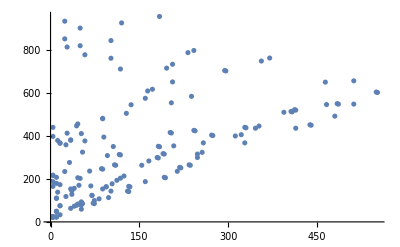

```mathematica
data=Transpose@{lefts,rights};
ListPlot[data]
```

```mathematica
rightsTruncated = rights[[1;;Length[rights]-1]]
```

{59,77,81,79,87,85,118,138,87,85,128,99,144,107,156,33,113,170,109,111,167,143,202,234,23,143,141,177,73,165,163,236,276,23,165,247,245,63,187,75,173,265,263,324,358,378,207,205,308,49,207,313,311,376,412,235,350,410,253,251,299,297,394,446,265,263,317,315,49,49,179,351,349,123,299,163,315,163,323,23,23,215,217,415,413,367,504,23,23,187,425,423,403,401,544,93,367,213,399,203,405,574,75,365,367,553,439,437,608,435,616,445,153,379,381,583,710,776,812,435,650,760,818,850,23,451,449,283,509,714,513,511,263,521,519,732,842,900,932,23,491,205,455,703,701,193,545,786,153,549,547,796,924,83,547,23,23,23,23,397,747,649,479,481,761,954,123,603,601,353,655,23,23,23}

```mathematica
leftsTruncated = lefts[[1;;Length[lefts]-1]]
```

{52,44,50,52,52,54,26,12,72,74,36,74,36,82,40,16,98,48,10,10,68,102,50,24,10,130,132,104,40,132,134,66,32,4,4,86,88,34,160,16,16,108,110,54,26,12,192,194,96,10,10,116,118,58,28,214,106,52,218,220,180,182,90,44,234,236,190,192,10,10,10,182,184,70,248,94,248,94,256,4,4,4,4,202,204,258,128,4,4,4,242,244,272,274,136,52,328,124,312,118,322,160,16,16,16,204,328,330,164,346,172,352,34,34,34,238,118,58,28,414,206,102,50,24,10,438,440,166,394,196,406,408,154,412,414,206,102,50,24,10,480,46,46,294,296,112,466,232,88,484,486,242,120,46,512,4,4,4,4,4,356,464,88,88,370,184,70,550,552,208,512,4,4,4}

```mathematica
Length[dStepNums]
```

174

```mathematica
Length[rightsTruncated]
```

174

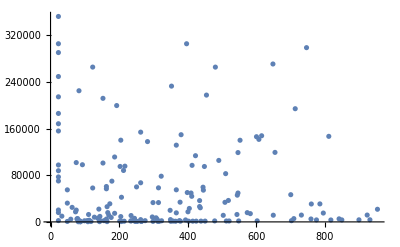

```mathematica
data2=Transpose@{rightsTruncated,dStepNums};
ListPlot[data2]
```

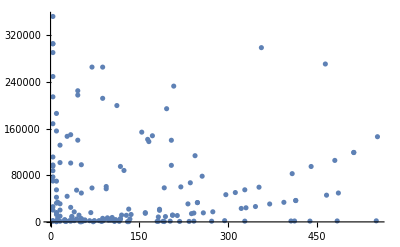

```mathematica
data3 = Transpose@{leftsTruncated,dStepNums};
ListPlot[data3]
```

```mathematica
sums = lefts + rights
```

{111,121,131,131,139,139,144,150,159,159,164,173,180,189,196,49,211,218,119,121,235,245,252,258,33,273,273,281,113,297,297,302,308,27,169,333,333,97,347,91,189,373,373,378,384,390,399,399,404,59,217,429,429,434,440,449,456,462,471,471,479,479,484,490,499,499,507,507,59,59,189,533,533,193,547,257,563,257,579,27,27,219,221,617,617,625,632,27,27,191,667,667,675,675,680,145,695,337,711,321,727,734,91,381,383,757,767,767,772,781,788,797,187,413,415,821,828,834,840,849,856,862,868,874,33,889,889,449,903,910,919,919,417,933,933,938,944,950,956,33,971,251,501,997,997,305,1011,1018,241,1033,1033,1038,1044,129,1059,27,27,27,27,401,1103,1113,567,569,1131,1138,193,1153,1153,561,1167,27,27,27,443}

```mathematica
sumsTruncated = sums[[1;;Length[sums]-1]]
```

{111,121,131,131,139,139,144,150,159,159,164,173,180,189,196,49,211,218,119,121,235,245,252,258,33,273,273,281,113,297,297,302,308,27,169,333,333,97,347,91,189,373,373,378,384,390,399,399,404,59,217,429,429,434,440,449,456,462,471,471,479,479,484,490,499,499,507,507,59,59,189,533,533,193,547,257,563,257,579,27,27,219,221,617,617,625,632,27,27,191,667,667,675,675,680,145,695,337,711,321,727,734,91,381,383,757,767,767,772,781,788,797,187,413,415,821,828,834,840,849,856,862,868,874,33,889,889,449,903,910,919,919,417,933,933,938,944,950,956,33,971,251,501,997,997,305,1011,1018,241,1033,1033,1038,1044,129,1059,27,27,27,27,401,1103,1113,567,569,1131,1138,193,1153,1153,561,1167,27,27,27}

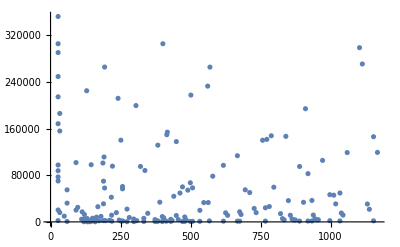

```mathematica
data4 = Transpose@{sumsTruncated,dStepNums};
ListPlot[data4]
```

```mathematica
(*Actually there were often more than two pieces*)
newRights = {59,77,81,79,87,85,118,138,87,85,128,99,144,107,156,158,113,170,113,111,167,143,202,234,236,143,141,177,180,165,163,236,276,278,159,247,245,246,187,190,179,265,263,324,358,378,207,205,308,310,207,313,311,376,412,235,350,410,253,251,299,297,394,446,265,263,317,315,257,255,339,351,349,350,299,302,315,318,323,293,379,395,393,415,413,367,504,506,321,471,425,423,403,401,544,546,367,370,399,402,405,574,576,373,371,553,439,437,608,435,616,445,448,405,403,583,710,776,812,435,650,760,818,850,852,451,449,450,509,714,513,511,512,521,519,732,842,900,932,934,491,494,491,703,701,702,545,786,788,549,547,796,924,926,547,550,535,745,743,697,747,649,561,559,761,954,956,603,601,602,655,658,589,825,765}
```

{59,77,81,79,87,85,118,138,87,85,128,99,144,107,156,158,113,170,113,111,167,143,202,234,236,143,141,177,180,165,163,236,276,278,159,247,245,246,187,190,179,265,263,324,358,378,207,205,308,310,207,313,311,376,412,235,350,410,253,251,299,297,394,446,265,263,317,315,257,255,339,351,349,350,299,302,315,318,323,293,379,395,393,415,413,367,504,506,321,471,425,423,403,401,544,546,367,370,399,402,405,574,576,373,371,553,439,437,608,435,616,445,448,405,403,583,710,776,812,435,650,760,818,850,852,451,449,450,509,714,513,511,512,521,519,732,842,900,932,934,491,494,491,703,701,702,545,786,788,549,547,796,924,926,547,550,535,745,743,697,747,649,561,559,761,954,956,603,601,602,655,658,589,825,765}

```mathematica
Length[newRights]
```

175

```mathematica
newRightsTruncated = newRights[[1;;Length[newRights]-1]]
```

{59,77,81,79,87,85,118,138,87,85,128,99,144,107,156,158,113,170,113,111,167,143,202,234,236,143,141,177,180,165,163,236,276,278,159,247,245,246,187,190,179,265,263,324,358,378,207,205,308,310,207,313,311,376,412,235,350,410,253,251,299,297,394,446,265,263,317,315,257,255,339,351,349,350,299,302,315,318,323,293,379,395,393,415,413,367,504,506,321,471,425,423,403,401,544,546,367,370,399,402,405,574,576,373,371,553,439,437,608,435,616,445,448,405,403,583,710,776,812,435,650,760,818,850,852,451,449,450,509,714,513,511,512,521,519,732,842,900,932,934,491,494,491,703,701,702,545,786,788,549,547,796,924,926,547,550,535,745,743,697,747,649,561,559,761,954,956,603,601,602,655,658,589,825}

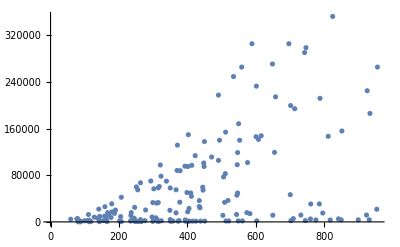

```mathematica
data5= Transpose@{newRightsTruncated,dStepNums};
ListPlot[data5]
```